## Basic conventions

Note that we use Φ for the orbital phase, hence
  Ω = dΦ/dt
  v = ((G M Ω)/c^3)^(1/3)
  x=v^2

```mathematica
m1=.;1;
m2=.;1;
χ1=.;{0,0,0};
χ2=.;{0,0,0};
M=m1+m2;
q=m1/m2;
ν=(m1 m2)/(m1+m2)^2;ν=(1-δ^2)/4;ν=q/(1+q)^2;
δ=(m1-m2)/(m1+m2);δ=(q-1)/(q+1);δ=√(1-4ν);
m1=(1+δ)/2;
m2=(1-δ)/2;
ℳ=M ν^(3/5);
χs=1/2(χ1+χ2);
χa=1/2(χ1-χ2);
Ln=.;{0,0,1};
```

```mathematica
χs=(χ1+χ2)/2;χs=1/2(S1/m1^2+S2/m2^2);χs=2(S1/(1+δ)^2+S2/(1-δ)^2);
χa=(χ1-χ2)/2;χa=1/2(S1/m1^2-S2/m2^2);χa=2(S1/(1+δ)^2-S2/(1-δ)^2);
```

For comparison with other references (esp. arXiv:0605140v4), we note the following definitions:
  S = S_1+S_2
  Σ=M(S_2/m_2-S_1/m_1)
Two particularly useful equalities are:
  S/M^2 = (S_1+S_2)/M^2=((χ_2(1-δ))^2+(χ_1(1+δ))^2)/4=(1-2ν)χ_s+δ χ_a
  Σ/M^2=(S_2/m_2-S_1/m_1)/M=(χ_2(1-δ)-χ_1(1+δ))/2=-δ χ_s-χ_a

#### Converting expressions for spins

```mathematica
FullSimplify[FullSimplify[(4/3(2- ν)χs+8/3 δ  χa)/.FullSimplify[Solve[{σl==-δ χs-χa,sl==(1-2ν)χs+δ χa},{χa,χs}][[1]]]/.{δ^2->1-4ν}]/.{δ^2->1-4ν}]
FullSimplify[FullSimplify[((8-(121 ν)/9+(2 ν^2)/9)χs+(8-(31 ν)/9)δ χa)/.FullSimplify[Solve[{σl==-δ χs-χa,sl==(1-2ν)χs+δ χa},{χa,χs}][[1]]]/.{δ^2->1-4ν}]/.{δ^2->1-4ν}]
FullSimplify[FullSimplify[((-11/4+3ν)χs-11/4 δ χa)/.FullSimplify[Solve[{σl==-δ χs-χa,sl==(1-2ν)χs+δ χa},{χa,χs}][[1]]]/.{δ^2->1-4ν}]/.{δ^2->1-4ν}]
FullSimplify[FullSimplify[((-59/16+(227 ν)/9-(157 ν^2)/9)χs+(-59/16+(701 ν)/36)δ χa)/.FullSimplify[Solve[{σl==-δ χs-χa,sl==(1-2ν)χs+δ χa},{χa,χs}][[1]]]/.{δ^2->1-4ν}]/.{δ^2->1-4ν}]
```

(14 sl)/3+2 δ σl

sl (11-(61 ν)/9)+1/3 δ (9-10 ν) σl

-4 sl-(5 δ σl)/4

sl (-9/2+(272 ν)/9)+1/16 δ (-13+172 ν) σl

```mathematica
FullSimplify[Simplify[((-16π sl-(31π)/6 δ σl)/.{σl->-δ χs-χa,sl->(1-2ν)χs+δ χa})]/.{δ^2->1-4ν}]
```

-1/6 π (65 δ χa+(65-68 ν) χs)

```mathematica
(* Energy expression from Eq.(4.6) of arXiv:1212.5520v1 *)
Expressions={(14/3 S+2δ Σ),(11-61/9 ν)S+δ(3-10/3 ν)Σ,(135/4-367/4 ν+29/12 ν^2)S+δ(27/4-39ν+5/4 ν^2)Σ};
For[i=1,i≤3,++i,
Print[Collect[Simplify[Expand[Expressions[[i]]/.{S->(1-2ν)χs+δ χa,Σ->-δ χs-χa}]]/.{δ^2->1-4ν},{χa,χs},FullSimplify]]
]
```

(8 δ χa)/3-4/3 (-2+ν) χs

δ (8-(31 ν)/9) χa+(8+1/9 ν (-121+2 ν)) χs

1/12 δ (324+ν (-633+14 ν)) χa+(27+1/12 ν (-1119+2 ν (172+ν))) χs

```mathematica
(* Magnitude of precession frequency from Eqs. (4.3) and (4.4) of arXiv:1212.5520v1 *)
```

```mathematica
Expressions={v^6 (7 Sn+3 δ Σn),v^8 (-3 Sn (1+4 ν)+1/2 δ (-6-11 ν) Σn),v^10 (1/2 Sn (-3-59 ν+18 ν^2)+1/24 δ (-36-231 ν+104 ν^2) Σn)};
For[i=1,i≤3,++i,
Print[Collect[Simplify[Expand[Expressions[[i]]/.{Sn->(1-2ν)χsn+δ χan,Σn->-δ χsn-χan}]]/.{δ^2->1-4ν},{v,χan,χsn},FullSimplify]]
]
```

v^6 (4 δ χan+(4-2 ν) χsn)

v^8 (-13/2 δ ν χan+1/2 ν (-25+4 ν) χsn)

v^10 (1/24 δ ν (-477+112 ν) χan-1/24 ν (549+4 ν (-151+4 ν)) χsn)

## Energy and flux definitions

We use Eqs. (C1--C13) http://arxiv.org/abs/0810.5336v3 [note the version number!], taking into account various errata on the spin-orbit terms, which can best be found in Eqs. (7.9) and (7.11) of arXiv:gr-qc/0605140v4 [note the version number!].  There are a additional SO terms from Eq. (6.2) of arxiv:1104.5659v1 and Eq. (4.6) of arXiv:1212.5520v1.  The occasionally used 4pN flux term comes from the extreme-mass-ratio limit [Eq. (43) of arXiv:gr-qc/9405062].

For flux and energy, non-spin terms are complete to 3.5pN order; SO terms are complete to 3.0pN in flux and 3.5pN in energy; SS terms are complete to 2.0pN.  The expression for the change in mass is complete to 3.0pN order.

```mathematica
Energy[0]:=-1/2 ν;
Energy[1]:=0;
Energy[2]:=-3/4-1/12 ν;
Energy[3]:=4/3(2- ν)(χs.Ln)+8/3 δ (χa.Ln);
Energy[4]:=(-27/8+19/8 ν-1/24 ν^2)+ν((χs.χs-χa.χa)-3((χs.Ln)^2-(χa.Ln)^2))+(1/2-ν)((χs.χs)+(χa.χa)-3((χs.Ln)^2+(χa.Ln)^2))+δ(χs.χa-3(χs.Ln)(χa.Ln));
Energy[5]:=(8-(121 ν)/9+(2 ν^2)/9)(χs.Ln)+(8-(31 ν)/9)δ(χa.Ln);
Energy[6]:=-675/64+(34445/576-205/96 π^2)ν-155/96 ν^2-35/5184 ν^3;
Energy[7]:=(27+1/12 ν (-1119+2 ν (172+ν))) (χs.Ln)+1/12 δ (324+ν (-633+14 ν)) (χa.Ln);
Unprotect[E];
E[v_]:=Energy[0] v^2(1+∑_(i=2)^7 Energy[i] v^i);
E[v_,Order_]:=Energy[0] v^2(1+∑_(i=2)^Min[Order,7] Energy[i] v^i);
Protect[E];

Flux[0,v_]:=32/5 ν^2;
Flux[1,v_]:=0;
Flux[2,v_]:=-1247/336-35/12 ν;
Flux[3,v_]:=4π+((-11/4+3ν)(χs.Ln)-11/4 δ(χa.Ln));
Flux[4,v_]:=(-44711/9072+9271/504 ν+65/18 ν^2)+(287/96+ν/24)(χs.Ln)^2-(89/96+(7ν)/24)(χs.χs)+(287/96-12ν)(χa.Ln)^2+(-89/96+4ν)(χa.χa)+287/48 δ(χs.Ln)(χa.Ln)-89/48 δ(χs.χa)(*+ν(-103/48(χs.χs-χa.χa)+289/48((χs.Ln)^2-(χa.Ln)^2)) This term was a duplicate in the original*);
Flux[5,v_]:=(-8191/672-583/24 ν)π+(-59/16+(227 ν)/9-(157 ν^2)/9)(χs.Ln)+(-59/16+(701 ν)/36)δ(χa.Ln);
Flux[6,v_]:=(6643739519/69854400+16/3 π^2-1712/105 EulerGamma-856/105 Log[16 v^2])+(-134543/7776+41/48 π^2)ν-94403/3024 ν^2-775/324 ν^3-π/6(65 δ(χa.Ln)+(65-68 ν)(χs.Ln));
Flux[7,v_]:=(-16285/504+214745/1728 ν+193385/3024 ν^2)π;
(* Note that the 4PN term below [Eq.(43) of arXiv:gr-qc/9405062] is not used normally; only when doing a Padé, for some reason. *)
Flux[8,v_]=-323105549467/3178375200-(1369 π^2)/126+(232597 EulerGamma)/4410+(39931 Log[2])/294-(47385 Log[3])/1568+(232597 Log[v])/4410;

ℱ[v_]:=Flux[0,v] v^10(1+∑_(i=2)^7 Flux[i,v] v^i);
ℱ8[v_]:=Flux[0,v] v^10(1+∑_(i=2)^8 Flux[i,v] v^i);
ℱ[v_,Order_]:=Flux[0,v] v^10(1+∑_(i=2)^Order Flux[i,v] v^i);

Mdot[v_]:=32/5 v^10 ν^2(-1/4 v^5 ((1-ν) δ χa.Ln(1+3 χa.χa+9 χs.χs)+(1-3 ν) χs.Ln(1+9 χa.χa+3 χs.χs)));
```

## TaylorT1

```mathematica
T1dEdvNum=Simplify[((ℱ[v]+Mdot[v])/(32/5 v^10 ν^2))/.{Ln->{0,0,1},Subscript[χ, a]->chia,Subscript[χ, s]->chis,χa->{0,0,chia},χs->{0,0,chis},Log[16 v^2]->2ln4v}]/.{ν->nu,δ->delta}
T1dEdvDen=Simplify[(E'[v]/.{Ln->{0,0,1},χa->{0,0,chia},χs->{0,0,chis}})/(-v ν)]/.{ν->nu,δ->delta}
```

1/209563200(209563200-623700 (1247+980 nu) v^2+52390800 (-11 chia delta+chis (-11+12 nu)+16 π) v^3-23100 (44711-37422 chia chis delta-166878 nu-32760 nu^2+567 chis^2 (-33+4 nu)+567 chia^2 (-33+128 nu)) v^4+103950 (4536 chia chis^2 delta (-1+nu)+1512 chis^3 (-1+3 nu)+14 chia delta (-567+108 chia^2 (-1+nu)+2840 nu)+14 chis (-567+3740 nu-2512 nu^2+324 chia^2 (-1+3 nu))-3 (8191+16324 nu) π) v^5-(-19931218557+3416878080 EulerGamma+3416878080 ln4v+3625933850 nu+6542127900 nu^2+501270000 nu^3+2270268000 chis π+2270268000 chia delta π-2375049600 chis nu π-1117670400 π^2-179001900 nu π^2) v^6+86625 (-78168+300643 nu+154708 nu^2) π v^7)

1-1/6 (9+nu) v^2+10/3 (2 chia delta-chis (-2+nu)) v^3+1/8 (-81-24 chia^2-24 chis^2-48 chia chis delta+57 nu+96 chia^2 nu-nu^2) v^4+7/18 (chia delta (72-31 nu)+chis (72-121 nu+2 nu^2)) v^5-(5 (10935+1674 nu^2+7 nu^3+9 nu (-6889+246 π^2)) v^6)/1296

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T1.txt"];
dvdtNum2=CForm[N[SeriesCoefficient[T1dEdvNum,{v,0,2}]]];
dvdtNum3=CForm[N[SeriesCoefficient[T1dEdvNum,{v,0,3}]]];
dvdtNum4=CForm[N[SeriesCoefficient[T1dEdvNum,{v,0,4}]]];
dvdtNum5=CForm[N[SeriesCoefficient[T1dEdvNum,{v,0,5}]]];
dvdtNum6=CForm[N[SeriesCoefficient[T1dEdvNum,{v,0,6}]/.ln4v->0]];
dvdtNum6Ln4v=CForm[N[D[SeriesCoefficient[T1dEdvNum,{v,0,6}],ln4v]]];
dvdtNum7=CForm[N[SeriesCoefficient[T1dEdvNum,{v,0,7}]]];
WriteString[OutFile,StringForm["      dvdtNum2(``),\n", dvdtNum2]]
WriteString[OutFile,StringForm["      dvdtNum3(``),\n", dvdtNum3]]
WriteString[OutFile,StringForm["      dvdtNum4(``),\n", dvdtNum4]]
WriteString[OutFile,StringForm["      dvdtNum5(``),\n", dvdtNum5]]
WriteString[OutFile,StringForm["      dvdtNum6(``),\n", dvdtNum6]]
WriteString[OutFile,StringForm["      dvdtNum6Ln4v(``),\n", dvdtNum6Ln4v]]
WriteString[OutFile,StringForm["      dvdtNum7(``),\n", dvdtNum7]]
dvdtDen2=CForm[N[SeriesCoefficient[T1dEdvDen,{v,0,2}]]];
dvdtDen3=CForm[N[SeriesCoefficient[T1dEdvDen,{v,0,3}]]];
dvdtDen4=CForm[N[SeriesCoefficient[T1dEdvDen,{v,0,4}]]];
dvdtDen5=CForm[N[SeriesCoefficient[T1dEdvDen,{v,0,5}]]];
dvdtDen6=CForm[N[SeriesCoefficient[T1dEdvDen,{v,0,6}]]];
WriteString[OutFile,StringForm["      dvdtDen2(``),\n", dvdtDen2]];
WriteString[OutFile,StringForm["      dvdtDen3(``),\n", dvdtDen3]];
WriteString[OutFile,StringForm["      dvdtDen4(``),\n", dvdtDen4]];
WriteString[OutFile,StringForm["      dvdtDen5(``),\n", dvdtDen5]];
WriteString[OutFile,StringForm["      dvdtDen6(``)\n", dvdtDen6]];
Close[OutFile];
```

Stiffness time: -34258.5 (should be less than t1=0.)

The final value of v: 0.504928

The plots start at: -430559.

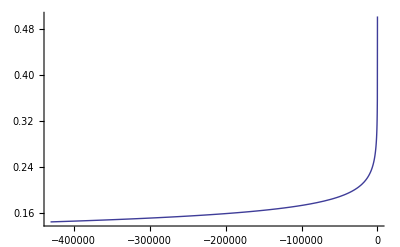

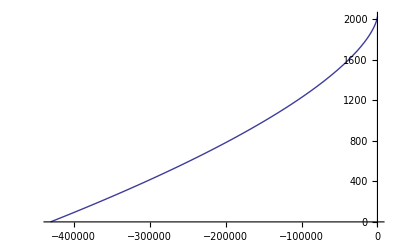

```mathematica
chis=0;
nu=1/4;
v0=0.144;
t0 =- 1.1 5/(256 nu v0^8); (* Guess this, and make sure the stiffness time below is less than t1. *)
t1 = 0.0;
T1dEdv[t_]:=((32/5 v^9 nu T1dEdvNum)/T1dEdvDen/.{ln4v->Log[4v]})/.v->v[t];
Quiet[T1Solution=NDSolve[{v'[t]==T1dEdv[t],v[t0]==v0,Φ'[t]==v[t]^3,Φ[t0]==0},{v,Φ},{t,t0,t1}]];
Print["Stiffness time: ",tOffset = T1Solution[[1,1,2,1,1,2]]," (should be less than t1=", t1, ")"]
Print["The final value of v: ", Evaluate[v[t1+tOffset]/.T1Solution][[1]]]
Print["The plots start at: ", t0-tOffset]
Plot[Evaluate[v[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->{All,{0,All}}]
Plot[Evaluate[Φ[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->All]
Clear[v0,nu,chis,t0,t1,m1,m2,S1,S2,χ1,χ2,Ln,M,ℳ,δ,χs,χa]
```

## TaylorT2

```mathematica
T2t=Collect[Expand[(256ν v^8)/5∫Normal[Series[E'[v]/(ℱ[v]+Mdot[v])/.{Ln->{0,0,1},Subscript[χ, a]->chia,Subscript[χ, s]->chis,χa->{0,0,chia},χs->{0,0,chis},δ->delta},{v,0,-2}]]ⅆv]/.{Log[v]->lnv},v,FullSimplify]/.ν->nu
T2Φ=Collect[Expand[32ν v^5∫Normal[Series[v^3 E'[v]/(ℱ[v]+Mdot[v])/.{Ln->{0,0,1},Subscript[χ, a]->chia,Subscript[χ, s]->chis,χa->{0,0,chia},χs->{0,0,chis},δ->delta},{v,0,1}]]ⅆv]/.{Log[v]->lnv},v,FullSimplify]/.ν->nu
```

1+(743/252+(11 nu)/3) v^2+2/15 (113 chia delta+chis (113-76 nu)-48 π) v^3+(3058673/508032-(81 chia chis delta)/4+1/8 chis^2 (-81+4 nu)+chia^2 (-81/8+40 nu)+1/504 nu (5429+4319 nu)) v^4+(chis^3 (2-6 nu)-2 chia^3 delta (-1+nu)-6 chia chis^2 delta (-1+nu)+1/756 chia delta (147101+6552 nu)+chis (147101/756+chia^2 (6-18 nu)-2/27 nu (2453+306 nu))+1/252 (-7729+1092 nu) π) v^5+1/1524096(chia delta (4074790483+504 (815049-1620346 nu) nu)-18144 chia^3 delta (19422+nu (-87455+2856 nu))-18144 chis^3 (19422+nu (-14929+10136 nu))-6096384 chia^2 (-57+224 nu) π+12 (-15419335+168 nu (-75703+29618 nu)) π-18144 chis^2 (chia delta (58266+nu (-39625+8568 nu))+336 (-57+4 nu) π)+chis (4074790483-3478848284 nu-1008 ((2237903-401548 nu) nu^2+18 chia^2 (13452+44814 delta^2+nu (-88271+100072 nu))-689472 chia delta π))) v^7+v^6 ((6848 EulerGamma)/105+(6848 lnv)/105+(-10052469856691+24236159077900 nu)/23471078400+1/672 chia^2 (-62763+69608 delta^2+56 nu (3431+3856 nu))+1/672 chis^2 (6845+4 nu (-43427+13720 nu))+2/3 chis (-227+156 nu) π-1/336 chia delta (chis (-6845+116312 nu)+50848 π)+(nu^2 (-45633+102260 nu)-432 (-512+451 nu) π^2)/5184+(3424 Log[16])/105)

1+(5 (743+924 nu) v^2)/1008+5/24 (113 chia delta+chis (113-76 nu)-48 π) v^3+(-405/8 chia chis delta+5/16 chis^2 (-81+4 nu)+5/16 chia^2 (-81+320 nu)+(5 (3058673+1008 nu (5429+4319 nu)))/1016064) v^4+1/2016 5 lnv (1512 chia^3 delta (-1+nu)+4536 chia chis^2 delta (-1+nu)+1512 chis^3 (-1+3 nu)-chia delta (147101+6552 nu)+chis (-147101+4536 chia^2 (-1+3 nu)+56 nu (2453+306 nu))+3 (7729-1092 nu) π) v^5+1/24385536 5 (18144 chia^3 delta (19422+nu (-87455+2856 nu))+18144 chis^3 (19422+nu (-14929+10136 nu))+chia delta (-4074790483+504 nu (-815049+1620346 nu))+6096384 chia^2 (-57+224 nu) π+12 (15419335+168 (75703-29618 nu) nu) π+18144 chis^2 (chia delta (58266+nu (-39625+8568 nu))+336 (-57+4 nu) π)+chis (-4074790483+3478848284 nu+1008 ((2237903-401548 nu) nu^2+18 chia^2 (13452+44814 delta^2+nu (-88271+100072 nu))-689472 chia delta π))) v^7+v^6 (-(1712 EulerGamma)/21-(1712 lnv)/21+(12348611926451-24236159077900 nu)/18776862720-(5 chia^2 (-62763+69608 delta^2+56 nu (3431+3856 nu)))/2688-(5 chis^2 (6845+4 nu (-43427+13720 nu)))/2688+5/6 chis (227-156 nu) π+(5 chia delta (chis (-6845+116312 nu)+50848 π))/1344+(5 ((45633-102260 nu) nu^2+432 (-512+451 nu) π^2))/20736-(856 Log[16])/21)

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T2.txt"];
t2=CForm[Collect[SeriesCoefficient[T2t,{v,0,2}],{chis,nu},N]];
t3=CForm[Collect[SeriesCoefficient[T2t,{v,0,3}],{chis,nu},N]];
t4=CForm[Collect[SeriesCoefficient[T2t,{v,0,4}],{chis,nu},N]];
t5=CForm[Collect[SeriesCoefficient[T2t,{v,0,5}],{chis,nu},N]];
t6=CForm[Collect[N[SeriesCoefficient[T2t,{v,0,6}]/.lnv->0],{chis,nu},N]];
t6Lnv=CForm[Collect[D[SeriesCoefficient[T2t,{v,0,6}],lnv],{chis,nu},N]];
t7=CForm[Collect[SeriesCoefficient[T2t,{v,0,7}],{chis,nu},N]];
WriteString[OutFile,StringForm["      t2(``),\n", t2]]
WriteString[OutFile,StringForm["      t3(``),\n", t3]]
WriteString[OutFile,StringForm["      t4(``),\n", t4]]
WriteString[OutFile,StringForm["      t5(``),\n", t5]]
WriteString[OutFile,StringForm["      t6(``),\n", t6]]
WriteString[OutFile,StringForm["      t6Lnv(``),\n", t6Lnv]]
WriteString[OutFile,StringForm["      t7(``),\n", t7]]
Phi2=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,2}],{chis,nu},N]];
Phi3=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,3}],{chis,nu},N]];
Phi4=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,4}],{chis,nu},N]];
Phi5=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,5}],{chis,nu},N]];
Phi5Lnv=CForm[Collect[D[SeriesCoefficient[T2Φ,{v,0,5}],lnv],{chis,nu},N]];
Phi6=CForm[Collect[N[SeriesCoefficient[T2Φ,{v,0,6}]/.lnv->0],{chis,nu},N]];
Phi6Lnv=CForm[Collect[D[SeriesCoefficient[T2Φ,{v,0,6}],lnv],{chis,nu},N]];
Phi7=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,7}],{chis,nu},N]];
WriteString[OutFile,StringForm["      Phi2(``),\n", Phi2]];
WriteString[OutFile,StringForm["      Phi3(``),\n", Phi3]];
WriteString[OutFile,StringForm["      Phi4(``),\n", Phi4]];
WriteString[OutFile,StringForm["      Phi5(``),\n", Phi5]];
WriteString[OutFile,StringForm["      Phi5Lnv(``),\n", Phi5Lnv]];
WriteString[OutFile,StringForm["      Phi6(``),\n", Phi6]];
WriteString[OutFile,StringForm["      Phi6Lnv(``),\n", Phi6Lnv]];
WriteString[OutFile,StringForm["      Phi7(``)\n"  , Phi7]];
Close[OutFile];
```

The plots start at: -430541.

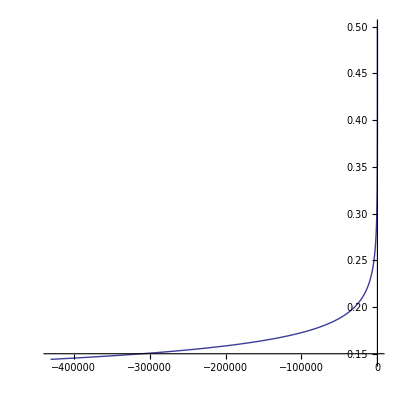

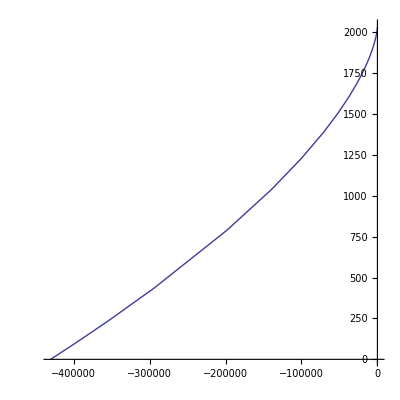

```mathematica
chis=0;
nu=1/4;
v0=0.144;
v1=0.5;
T2tFunc[va_]=(-5/(256nu va^8)T2t/.{v->va,lnv->Log[va]});
T2PhiFunc[va_]=(1/(32nu va^5)T2Φ/.{v->va,lnv->Log[va]});
Print["The plots start at: ",T2tFunc[v0]]
ParametricPlot[{T2tFunc[v],v},{v,v0,v1},AspectRatio->1,PlotRange->All]
ParametricPlot[{T2tFunc[v],T2PhiFunc[v0]-T2PhiFunc[v]},{v,v0,v1},AspectRatio->1,PlotRange->All]
Clear[v0,v1,nu,chis]
```

## TaylorT3

```mathematica
τ[ν_,t_,t0_]:=ν/5(t0-t);
T3vA[τ_]=Assuming[nu>0,Collect[Normal[
InverseSeries[Series[((5/(256nu v^8)Collect[Expand[(256nu v^8)/5∫Normal[Series[E'[v]/(ℱ[v]+Mdot[v])/.{Ln->{0,0,1},Subscript[χ, a]->chia,Subscript[χ, s]->chis,χa->{0,0,chia},χs->{0,0,chis},δ->delta,ν->nu},{v,0,-2}]]ⅆv],v,FullSimplify]))/.{((3424 Log[16])/105+(6848 Log[v])/105)->(-(856 Log[τ/256])/105)},{v,0,-1}],T]]/.{T->(5τ/nu)},v,Simplify]];
T3vA[τ_]=(Normal[Series[T3vA[T^-8],{T,0,8}]]/.{T->τ^(-1/8),ν->nu});
T3ΦA[τ_]=-Collect[∫Collect[Normal[Series[(5 T3vA[T^-8]^3)/nu,{T,0,10}]]/.{T->τ^(-1/8)},τ]ⅆτ,τ]/.{ν->nu,Log[τ]->lntau};
T3v=Collect[Simplify[2/τToNegativeOne8th T3vA[τToNegativeOne8th^-8],Assumptions->{τToNegativeOne8th>0}],τToNegativeOne8th]/.{Log[τToNegativeOne8th]->(-1/8)lntau}
T3Φ=Collect[Simplify[-nu τToNegativeOne8th^5 T3ΦA[τToNegativeOne8th^-8],Assumptions->{τToNegativeOne8th>0}],τToNegativeOne8th]
```

1+((743+924 nu) τToNegativeOne8th^2)/8064+1/480 (113 chia delta+chis (113-76 nu)-48 π) τToNegativeOne8th^3+1/130056192(4461199-20575296 chia chis delta+6825672 nu+6145776 nu^2+127008 chis^2 (-81+4 nu)+127008 chia^2 (-81+320 nu)) τToNegativeOne8th^4-1/1935360(15120 chia^3 delta (-1+nu)+45360 chia chis^2 delta (-1+nu)+15120 chis^3 (-1+3 nu)+chia delta (-1387051+38892 nu)+chis (-1387051+1421624 nu+101136 nu^2+45360 chia^2 (-1+3 nu))+6 (32701-12852 nu) π) τToNegativeOne8th^5-1/1560674304(18144 chia^3 delta (19422-87455 nu+2856 nu^2)+18144 chis^3 (19422-14929 nu+10136 nu^2)+chia delta (-4074790483-410784696 nu+816654384 nu^2)+6096384 chia^2 (-57+224 nu) π+12 (15419335+12718104 nu-4975824 nu^2) π+chis (-4074790483+3478848284 nu+2255806224 nu^2-404760384 nu^3+18144 chia^2 (13452+44814 delta^2-88271 nu+100072 nu^2)-694987776 chia delta π)+18144 chis^2 (chia delta (58266-39625 nu+8568 nu^2)+336 (-57+4 nu) π)) τToNegativeOne8th^7+1/288412611379200 τToNegativeOne8th^6 (-242170811046259+36738273116160 EulerGamma-4592284139520 lntau+579139571772300 nu-7948730235600 nu^2+9550175342400 nu^3+1397088 chis^2 (-108937-94733152 nu+30247952 nu^2)+1397088 chia^2 (36044288 delta^2+25 (-1446129+4448348 nu+4886784 nu^2))+15021490176 chis (-5223+3596 nu) π+22592321224704 π^2-21170912716800 nu π^2-2794176 chia delta (chis (108937+64068676 nu)+28078848 π)+4592284139520 Log[256])

1+(5 (743+924 nu) τToNegativeOne8th^2)/8064+1/64 (113 chia delta+chis (113-76 nu)-48 π) τToNegativeOne8th^3+1/14450688 5 (1855099-6858432 chia chis delta+3190600 nu+2617776 nu^2+42336 chis^2 (-81+4 nu)+42336 chia^2 (-81+320 nu)) τToNegativeOne8th^4-1/516096 5 lntau (1512 chia^3 delta (-1+nu)+4536 chia chis^2 delta (-1+nu)+1512 chis^3 (-1+3 nu)-chia delta (147101+6552 nu)+chis (-147101+137368 nu+17136 nu^2+4536 chia^2 (-1+3 nu))+3 (7729-1092 nu) π) τToNegativeOne8th^5+1/520224768(756 chia^3 delta (1350103-6008470 nu+180600 nu^2)+756 chis^3 (1350103-1021458 nu+642264 nu^2)+2 chia delta (-5386538891-884569035 nu+980367696 nu^2)+2286144 chia^2 (-407+1600 nu) π+3 (188516689+164245200 nu-47634384 nu^2) π+2 chis (-5386538891+4258127587 nu+3156448596 nu^2-449340192 nu^3+1134 chia^2 (325681+1024422 delta^2-2048582 nu+2199400 nu^2)-930460608 chia delta π)+2268 chis^2 (chia delta (1350103-883658 nu+180600 nu^2)+1008 (-407+28 nu) π)) τToNegativeOne8th^7+1/57682522275840 τToNegativeOne8th^6 (831032450749357-110214819348480 EulerGamma+13776852418560 lntau-1753429845806100 nu+4858670401200 nu^2-38454265080000 nu^3-4191264 chis^2 (8322937-113716448 nu+35608048 nu^2)-4191264 chia^2 (47485312 delta^2+25 (-1566495+4774180 nu+5478144 nu^2))-45064470528 chis (-6127+4204 nu) π-76429342015488 π^2+63512738150400 nu π^2+58677696 chia delta (chis (-1188991+10786532 nu)+4705536 π)-13776852418560 Log[256])

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T3.txt"];
v2=CForm[N[SeriesCoefficient[T3v,{τToNegativeOne8th,0,2}]]];
v3=CForm[N[SeriesCoefficient[T3v,{τToNegativeOne8th,0,3}]]];
v4=CForm[N[SeriesCoefficient[T3v,{τToNegativeOne8th,0,4}]]];
v5=CForm[N[SeriesCoefficient[T3v,{τToNegativeOne8th,0,5}]]];
v6=CForm[N[SeriesCoefficient[T3v,{τToNegativeOne8th,0,6}]/.lntau->0]];
v6lntau=CForm[N[D[SeriesCoefficient[T3v,{τToNegativeOne8th,0,6}],lntau]]];
v7=CForm[N[SeriesCoefficient[T3v,{τToNegativeOne8th,0,7}]]];
WriteString[OutFile,StringForm["      v2(``),\n", v2/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v3(``),\n", v3/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v4(``),\n", v4/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v5(``),\n", v5/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v6(``),\n", v6/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v6lntau(``),\n", v6lntau/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v7(``),\n", v7/.τToNegativeOne8th->taum8]]
Phi2=CForm[N[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,2}]]];
Phi3=CForm[N[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,3}]]];
Phi4=CForm[N[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,4}]]];
Phi5lntau=CForm[N[D[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,5}],lntau]]];
Phi6=CForm[N[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,6}]/.lntau->0]];
Phi6lntau=CForm[N[D[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,6}],lntau]]];
Phi7=CForm[N[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,7}]]];
WriteString[OutFile,StringForm["      Phi2(``),\n", Phi2/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi3(``),\n", Phi3/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi4(``),\n", Phi4/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi5lntau(``),\n", Phi5lntau/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi6(``),\n", Phi6/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi6lntau(``),\n", Phi6lntau/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi7(``)\n", Phi7/.τToNegativeOne8th->taum8]]
Close[OutFile];
```

The plots start at -410909.M and goes to -10M

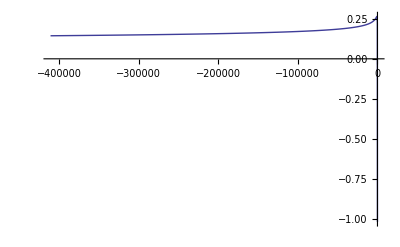

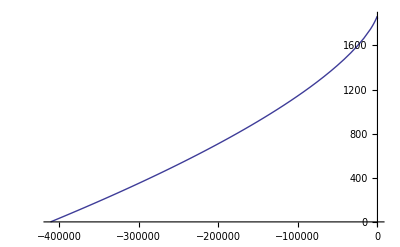

```mathematica
chis=-0.94905;
chia=0;
q=1;
delta=(q-1)/(q+1);
nu=q/(1+q)^2;
t0=0;
tf=t0-10;
T3vFunc[t_]=((τToNegativeOne8th/2 T3v)/.{τToNegativeOne8th->τ[nu,t,t0]^(-1/8),lntau->Log[τ[nu,t,t0]]});
T3PhiFunc[t_]=((-1/(nu τToNegativeOne8th^5)T3Φ)/.{τToNegativeOne8th->τ[nu,t,t0]^(-1/8),lntau->Log[τ[nu,t,t0]]});
v0=0.144;
v1=0.5;
ti=Chop[t/.FindRoot[T3vFunc[t]==v0,{t,-5/(256 nu v0^8)}][[1]]];
Print["The plots start at ",ti,"M and goes to ",tf,"M"]
Plot[T3vFunc[t],{t,ti,tf},PlotRange->All]
Plot[T3PhiFunc[t]-T3PhiFunc[ti],{t,ti,tf},PlotRange->All]
Clear[v0,v1,q,delta,nu,chis,chia,t0,ti,tf]
```

## TaylorT4

```mathematica
T4dEdv=Collect[5/(32ν v^9)Series[Simplify[-(ℱ[v]+Mdot[v])/D[E[v],v]/.{Ln->{0,0,1},Subscript[χ, a]->chia,Subscript[χ, s]->chis,χa->{0,0,chia},χs->{0,0,chis},Log[16 v^2]->2ln4v,δ->delta}],{v,0,16}],{v,χa,χs,ν},FullSimplify]/.ν->nu
```

1+(-743/336-(11 nu)/4) v^2+(-113/12 (chis+chia delta)+(19 chis nu)/3+4 π) v^3+(34103/18144+(81 chis^2)/16+81/16 chia (chia+2 chis delta)+(13661/2016-20 chia^2-chis^2/4) nu+(59 nu^2)/18) v^4+(-(79 chis nu^2)/3+(-2 chis (31571+2268 chia^2+756 chis^2)-2 chia (31571+756 chia^2+2268 chis^2) delta-12477 π)/2016+1/24 nu ((46328/21+162 chia^2) chis+54 chis^3+1165 chia delta+18 chia^3 delta+54 chia chis^2 delta-567 π)) v^5+(16447322263/139708800+(128495 chis^2)/2016+(5 chia (51398 chis delta+chia (387+25312 delta^2)))/2016-(1712 EulerGamma)/105-(1712 ln4v)/105+(541/896+(89 chia^2)/3+(1517 chis^2)/72) nu^2-(5605 nu^3)/2592-75/2 (chis+chia delta) π+(16 π^2)/3+nu (-56198689/217728-(2435 chia^2)/224-(23441 chis^2)/288-(12733 chia chis delta)/144+(74 chis π)/3+(451 π^2)/48)) v^6+(-(505 chis^3)/8-(2529407 chia delta)/27216-(505 chia^3 delta)/8+(2045 chis nu^3)/216-(4415 π)/4032+12 chia^2 π+chis^2 (-(1515 chia delta)/8+12 π)+(nu^2 (-3 chis (398017+285348 chia^2+924 chis^2)+7 chia (-41551+108 chia^2+324 chis^2) delta+365980 π))/6048+nu ((10772921/54432+(7007 chia^2)/24) chis+(979 chis^3)/24+(845827 chia delta)/6048+(742 chia^3 delta)/3+917/12 chia chis^2 delta+(358675 π)/6048-48 chia^2 π)+chis (-2529407/27216-1/8 chia^2 (523+992 delta^2)+24 chia delta π)) v^7

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T4.txt"];
dvdt2=CForm[N[SeriesCoefficient[T4dEdv,{v,0,2}]]];
dvdt3=CForm[N[SeriesCoefficient[T4dEdv,{v,0,3}]]];
dvdt4=CForm[N[SeriesCoefficient[T4dEdv,{v,0,4}]]];
dvdt5=CForm[N[SeriesCoefficient[T4dEdv,{v,0,5}]]];
dvdt6=CForm[N[SeriesCoefficient[T4dEdv,{v,0,6}]/.ln4v->0]];
dvdt6Ln4v=CForm[N[D[SeriesCoefficient[T4dEdv,{v,0,6}],ln4v]]];
dvdt7=CForm[N[SeriesCoefficient[T4dEdv,{v,0,7}]]];
WriteString[OutFile,StringForm["      dvdt2(``),\n", dvdt2]]
WriteString[OutFile,StringForm["      dvdt3(``),\n", dvdt3]]
WriteString[OutFile,StringForm["      dvdt4(``),\n", dvdt4]]
WriteString[OutFile,StringForm["      dvdt5(``),\n", dvdt5]]
WriteString[OutFile,StringForm["      dvdt6(``),\n", dvdt6]]
WriteString[OutFile,StringForm["      dvdt6Ln4v(``),\n", dvdt6Ln4v]]
WriteString[OutFile,StringForm["      dvdt7(``)\n", dvdt7]]
Close[OutFile];
```

Stiffness time: -34083.9 (should be less than t1=0.)

The final value of v: 2.08746

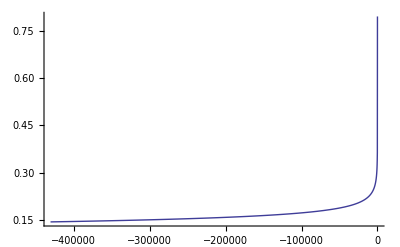

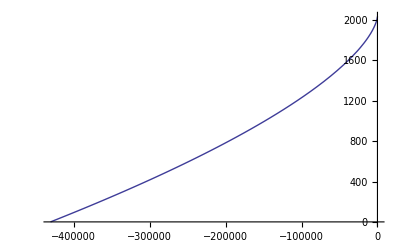

```mathematica
chis=0;
nu=1/4;
v0=0.144;
t0 =- 1.1 5/(256 nu v0^8); (* Guess this, and make sure the stiffness time below is less than t1. *)
t1 = 0.0;
T4dEdvFunc[t_]:=(32/5 v^9 nu T4dEdv/.{ln4v->Log[4v]})/.v->v[t];
Quiet[T1Solution=NDSolve[{v'[t]==T4dEdvFunc[t],v[t0]==v0,Φ'[t]==v[t]^3,Φ[t0]==0},{v,Φ},{t,t0,t1}]];
Print["Stiffness time: ",tOffset = T1Solution[[1,1,2,1,1,2]]," (should be less than t1=", t1, ")"]
Print["The final value of v: ", Evaluate[v[t1+tOffset]/.T1Solution][[1]]]
Plot[Evaluate[v[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->{All,{0,All}}]
Plot[Evaluate[Φ[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->All]
Clear[v0,nu,chis,t0,t1,m1,m2,S1,S2,χ1,χ2,Ln,M,ℳ,δ,χs,χa]
```

## TaylorT4Spin

```mathematica
T4dEdv=Collect[5/(32ν v^9)Series[Simplify[-(ℱ[v]+Mdot[v])/D[E[v],v]/.{χs.χs->chischis,χs.χa->chischia,χa.Ln->chiaLNHat,χa.χa->chiachia,χs.Ln->chisLNHat,Log[16 v^2]->2ln4v,δ->delta}],{v,0,16}],{v,χa,χs,ν},FullSimplify]/.ν->nu
```

1+(-743/336-(11 nu)/4) v^2+(-113/12 (chisLN+chiaLN delta)+(19 chisLN nu)/3+4 π) v^3+(1/18144(34103-44037 chiachia-44037 chischis+135891 chisLN^2-88074 chischia delta+135891 chiaLN (chiaLN+2 chisLN delta))+(10 chiachia-30 chiaLN^2+(13661-588 chischis+84 chisLN^2)/2016) nu+(59 nu^2)/18) v^4+(-(79 chisLN nu^2)/3+nu ((5791/63+(27 chiachia)/4+(9 chischis)/4) chisLN+1/24 (chiaLN (1165+18 chiachia+54 chischis) delta-567 π))+(-2 (31571+2268 chiachia+756 chischis) chisLN-2 chiaLN (31571+756 chiachia+2268 chischis) delta-12477 π)/2016) v^5+(16447322263/139708800-(145 chiachia)/448-(145 chischis)/448+(258295 chisLN^2)/4032-(145 chischia delta)/224+(5 chiaLN (103318 chisLN delta+chiaLN (1035+50624 delta^2)))/4032-(1712 EulerGamma)/105-(1712 ln4v)/105+(541/896-(89 chiachia)/6+(89 chiaLN^2)/2-(7 chischis)/144+(3041 chisLN^2)/144) nu^2-(5605 nu^3)/2592-75/2 (chisLN+chiaLN delta) π+(16 π^2)/3+nu (1/217728(-56198689+1187190 chiachia+714798 chischis-18436194 chisLN^2+1620108 chischia delta-54 chiaLN (65815 chiaLN+386526 chisLN delta))+(74 chisLN π)/3+(451 π^2)/48)) v^6+(1/27216(-2512188 chisLN^3-7536564 chiaLN chisLN^2 delta+chiaLN delta (-2529407+794178 chiachia-2512188 chiaLN^2+732942 chischis+1649592 chischia delta)+chisLN (-2529407+732942 chiachia+794178 chischis+1649592 chischia delta-2512188 chiaLN^2 (1+2 delta^2)))+(2045 chisLN nu^3)/216-(4415 π)/4032-6 (chiachia+chischis-3 chisLN^2+2 chischia delta-3 chiaLN (chiaLN+2 chisLN delta)) π+1/6048 nu^2 (3 (-398017+146076 chiachia-431424 chiaLN^2-1204 chischis) chisLN+840 chisLN^3+7 chiaLN (-41551+108 chiachia+324 chischis) delta+365980 π)+nu ((851 chisLN^3)/16+(739 chiaLN^3 delta)/2+(chiaLN (845827-738864 chiachia+29904 chischis) delta)/6048+7679/72 chiaLN chisLN^2 delta-(chisLN (-10772921+7130970 chiachia-23022846 chiaLN^2+674730 chischis+1914948 chischia delta))/54432+(358675 π)/6048+24 chiachia π-72 chiaLN^2 π)) v^7

```mathematica
SetDirectory["/Users/boyle/Research/Triton_IS_FOR_OLD_DATA/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T4Spin.txt"];
dvdt2=CForm[N[SeriesCoefficient[T4dEdv,{v,0,2}]]];
dvdt3=CForm[N[SeriesCoefficient[T4dEdv,{v,0,3}]]];
dvdt4=CForm[N[SeriesCoefficient[T4dEdv,{v,0,4}]]];
dvdt5=CForm[N[SeriesCoefficient[T4dEdv,{v,0,5}]]];
dvdt6=CForm[N[SeriesCoefficient[T4dEdv,{v,0,6}]/.ln4v->0]];
dvdt6Ln4v=CForm[N[D[SeriesCoefficient[T4dEdv,{v,0,6}],ln4v]]];
dvdt7=CForm[N[SeriesCoefficient[T4dEdv,{v,0,7}]]];
WriteString[OutFile,StringForm["      dvdt2(``),\n", dvdt2]]
WriteString[OutFile,StringForm["      dvdt3(``),\n", dvdt3]]
WriteString[OutFile,StringForm["      dvdt4(``),\n", dvdt4]]
WriteString[OutFile,StringForm["      dvdt5(``),\n", dvdt5]]
WriteString[OutFile,StringForm["      dvdt6(``),\n", dvdt6]]
WriteString[OutFile,StringForm["      dvdt6Ln4v(``),\n", dvdt6Ln4v]]
WriteString[OutFile,StringForm["      dvdt7(``)\n", dvdt7]]
Close[OutFile];
```

```mathematica
chis=0;
nu=1/4;
v0=0.144;
t0 =- 1.1 5/(256 nu v0^8); (* Guess this, and make sure the stiffness time below is less than t1. *)
t1 = 0.0;
T4dEdvFunc[t_]:=(32/5 v^9 nu T4dEdv/.{ln4v->Log[4v]})/.v->v[t];
Quiet[T1Solution=NDSolve[{v'[t]==T4dEdvFunc[t],v[t0]==v0,Φ'[t]==v[t]^3,Φ[t0]==0},{v,Φ},{t,t0,t1}]];
Print["Stiffness time: ",tOffset = T1Solution[[1,1,2,1,1,2]]," (should be less than t1=", t1, ")"]
Print["The final value of v: ", Evaluate[v[t1+tOffset]/.T1Solution][[1]]]
Plot[Evaluate[v[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->{All,{0,All}}]
Plot[Evaluate[Φ[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->All]
Clear[v0,nu,chis,t0,t1,m1,m2,S1,S2,χ1,χ2,Ln,M,ℳ,δ,χs,χa]
```

Stiffness time: -34083.9 (should be less than t1=0.)

The final value of v: 2.08746

-Graphics-

-Graphics-

## Taylor Flux

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes"];
OutFile = OpenWrite["Flux_Taylor_Coefficients.txt"];
For[i=0,i≤8,i++,
Term = FullSimplify[Flux[i,v]/.{Log[16 v^2]->4Log[2]+2lnv,Log[v]->lnv,Ln->{0,0,1},χa->{0,0,chia},χs->{0,0,chis},ν->nu,δ->delta}];
If[(Term/.lnv->0)=!=0,
WriteString[OutFile,StringForm["    F``(``),\n",i,CForm[N[FullSimplify[Term/.lnv->0]]]]];
]
If[D[Term,lnv]=!=0,
WriteString[OutFile,StringForm["    F``lnv(``),\n",i,CForm[N[FullSimplify[D[Term,lnv]]]]]];
]
]
Close[OutFile];
```

## Padé flux

For some reason, it is standard to include the EMRI-limit 4PN term in the flux when using Padé expressions (but at no other times).

### Log - constant

This version treats logarithms as if they were constant [see, e.g., Sec. III of Mroué et al.,  PRD 78, 044004].

```mathematica
(* Note that f1=0 in this case *)
ℱPadeLogConst[v_]:=Flux[0,v] v^10(1+f2 v^2+f3 v^3+f4 v^4+f5 v^5+(f6+f6lnv  lnv)v^6+f7 v^7+(f8+f8lnv  lnv)v^8);
PadeFlux44LogConst=HornerForm[PadeApproximant[1+f2 v^2+f3 v^3+f4 v^4+f5 v^5+(f6+f6lnv  lnv)v^6+f7 v^7+(f8+f8lnv  lnv)v^8,{v,0,{4,4}}],v];
PadeFlux44LogConstNum=(f4^4-3 f3 f4^2 f5+f3^2 f5^2+2 f2 f4 f5^2+2 f3^2 f4 f6-2 f2 f4^2 f6-2 f2 f3 f5 f6+f2^2 f6^2-f3^3 f7+2 f2 f3 f4 f7-f2^2 f5 f7+2 f3^2 f4 f6lnv lnv-2 f2 f4^2 f6lnv lnv-2 f2 f3 f5 f6lnv lnv+2 f2^2 f6 f6lnv lnv+f2^2 f6lnv^2 lnv^2+v (-f4^3 f5+2 f3 f4 f5^2-f2 f5^3+f3 f4^2 f6-2 f3^2 f5 f6+f2 f3 f6^2-f3^2 f4 f7+f2 f4^2 f7+f2 f3 f5 f7-f2^2 f6 f7+f3^3 f8-2 f2 f3 f4 f8+f2^2 f5 f8+f3 f4^2 f6lnv lnv-2 f3^2 f5 f6lnv lnv+2 f2 f3 f6 f6lnv lnv-f2^2 f6lnv f7 lnv+f3^3 f8lnv lnv-2 f2 f3 f4 f8lnv lnv+f2^2 f5 f8lnv lnv+f2 f3 f6lnv^2 lnv^2+v (f2 f4^4-3 f2 f3 f4^2 f5+f2 f3^2 f5^2+2 f2^2 f4 f5^2+f4^2 f5^2-f3 f5^3+2 f2 f3^2 f4 f6-2 f2^2 f4^2 f6-f4^3 f6-2 f2^2 f3 f5 f6+f2 f5^2 f6+f2^3 f6^2+f2 f4 f6^2-f2 f3^3 f7+2 f2^2 f3 f4 f7+f3 f4^2 f7-f2^3 f5 f7+f3^2 f5 f7-3 f2 f4 f5 f7-f2 f3 f6 f7+f2^2 f7^2-f3^2 f4 f8+f2 f4^2 f8+f2 f3 f5 f8-f2^2 f6 f8+2 f2 f3^2 f4 f6lnv lnv-2 f2^2 f4^2 f6lnv lnv-f4^3 f6lnv lnv-2 f2^2 f3 f5 f6lnv lnv+f2 f5^2 f6lnv lnv+2 f2^3 f6 f6lnv lnv+2 f2 f4 f6 f6lnv lnv-f2 f3 f6lnv f7 lnv-f2^2 f6lnv f8 lnv-f3^2 f4 f8lnv lnv+f2 f4^2 f8lnv lnv+f2 f3 f5 f8lnv lnv-f2^2 f6 f8lnv lnv+f2^3 f6lnv^2 lnv^2+f2 f4 f6lnv^2 lnv^2-f2^2 f6lnv f8lnv lnv^2+v (f3 f4^4-3 f3^2 f4^2 f5-f2 f4^3 f5+f3^3 f5^2+4 f2 f3 f4 f5^2-f2^2 f5^3-f4 f5^3+2 f3^3 f4 f6-f2 f3 f4^2 f6-4 f2 f3^2 f5 f6+2 f4^2 f5 f6+f3 f5^2 f6+2 f2^2 f3 f6^2-2 f3 f4 f6^2-f2 f5 f6^2-f3^4 f7+f2 f3^2 f4 f7+f2^2 f4^2 f7-f4^3 f7+f2 f5^2 f7-f2^3 f6 f7+f3^2 f6 f7+f2 f4 f6 f7-f2 f3 f7^2+f2 f3^3 f8-2 f2^2 f3 f4 f8+f3 f4^2 f8+f2^3 f5 f8-f3^2 f5 f8-f2 f4 f5 f8+f2 f3 f6 f8+2 f3^3 f4 f6lnv lnv-f2 f3 f4^2 f6lnv lnv-4 f2 f3^2 f5 f6lnv lnv+2 f4^2 f5 f6lnv lnv+f3 f5^2 f6lnv lnv+4 f2^2 f3 f6 f6lnv lnv-4 f3 f4 f6 f6lnv lnv-2 f2 f5 f6 f6lnv lnv-f2^3 f6lnv f7 lnv+f3^2 f6lnv f7 lnv+f2 f4 f6lnv f7 lnv+f2 f3 f6lnv f8 lnv+f2 f3^3 f8lnv lnv-2 f2^2 f3 f4 f8lnv lnv+f3 f4^2 f8lnv lnv+f2^3 f5 f8lnv lnv-f3^2 f5 f8lnv lnv-f2 f4 f5 f8lnv lnv+f2 f3 f6 f8lnv lnv+2 f2^2 f3 f6lnv^2 lnv^2-2 f3 f4 f6lnv^2 lnv^2-f2 f5 f6lnv^2 lnv^2+f2 f3 f6lnv f8lnv lnv^2+(f4^5-4 f3 f4^3 f5+3 f3^2 f4 f5^2+3 f2 f4^2 f5^2-2 f2 f3 f5^3+f5^4+3 f3^2 f4^2 f6-3 f2 f4^3 f6-2 f3^3 f5 f6-2 f2 f3 f4 f5 f6+f2^2 f5^2 f6-3 f4 f5^2 f6+f2 f3^2 f6^2+2 f2^2 f4 f6^2+f4^2 f6^2+2 f3 f5 f6^2-f2 f6^3-2 f3^3 f4 f7+4 f2 f3 f4^2 f7+2 f2 f3^2 f5 f7-4 f2^2 f4 f5 f7+2 f4^2 f5 f7-2 f3 f5^2 f7-2 f2^2 f3 f6 f7-2 f3 f4 f6 f7+2 f2 f5 f6 f7+f2^3 f7^2+f3^2 f7^2-f2 f4 f7^2+f3^4 f8-3 f2 f3^2 f4 f8+f2^2 f4^2 f8-f4^3 f8+2 f2^2 f3 f5 f8+2 f3 f4 f5 f8-f2 f5^2 f8-f2^3 f6 f8-f3^2 f6 f8+f2 f4 f6 f8+3 f3^2 f4^2 f6lnv lnv-3 f2 f4^3 f6lnv lnv-2 f3^3 f5 f6lnv lnv-2 f2 f3 f4 f5 f6lnv lnv+f2^2 f5^2 f6lnv lnv-3 f4 f5^2 f6lnv lnv+2 f2 f3^2 f6 f6lnv lnv+4 f2^2 f4 f6 f6lnv lnv+2 f4^2 f6 f6lnv lnv+4 f3 f5 f6 f6lnv lnv-3 f2 f6^2 f6lnv lnv-2 f2^2 f3 f6lnv f7 lnv-2 f3 f4 f6lnv f7 lnv+2 f2 f5 f6lnv f7 lnv-f2^3 f6lnv f8 lnv-f3^2 f6lnv f8 lnv+f2 f4 f6lnv f8 lnv+f3^4 f8lnv lnv-3 f2 f3^2 f4 f8lnv lnv+f2^2 f4^2 f8lnv lnv-f4^3 f8lnv lnv+2 f2^2 f3 f5 f8lnv lnv+2 f3 f4 f5 f8lnv lnv-f2 f5^2 f8lnv lnv-f2^3 f6 f8lnv lnv-f3^2 f6 f8lnv lnv+f2 f4 f6 f8lnv lnv+f2 f3^2 f6lnv^2 lnv^2+2 f2^2 f4 f6lnv^2 lnv^2+f4^2 f6lnv^2 lnv^2+2 f3 f5 f6lnv^2 lnv^2-3 f2 f6 f6lnv^2 lnv^2-f2^3 f6lnv f8lnv lnv^2-f3^2 f6lnv f8lnv lnv^2+f2 f4 f6lnv f8lnv lnv^2-f2 f6lnv^3 lnv^3) v))));
PadeFlux44LogConstDen=(f4^4-3 f3 f4^2 f5+f3^2 f5^2+2 f2 f4 f5^2+2 f3^2 f4 f6-2 f2 f4^2 f6-2 f2 f3 f5 f6+f2^2 f6^2-f3^3 f7+2 f2 f3 f4 f7-f2^2 f5 f7+2 f3^2 f4 f6lnv lnv-2 f2 f4^2 f6lnv lnv-2 f2 f3 f5 f6lnv lnv+2 f2^2 f6 f6lnv lnv+f2^2 f6lnv^2 lnv^2+v (-f4^3 f5+2 f3 f4 f5^2-f2 f5^3+f3 f4^2 f6-2 f3^2 f5 f6+f2 f3 f6^2-f3^2 f4 f7+f2 f4^2 f7+f2 f3 f5 f7-f2^2 f6 f7+f3^3 f8-2 f2 f3 f4 f8+f2^2 f5 f8+f3 f4^2 f6lnv lnv-2 f3^2 f5 f6lnv lnv+2 f2 f3 f6 f6lnv lnv-f2^2 f6lnv f7 lnv+f3^3 f8lnv lnv-2 f2 f3 f4 f8lnv lnv+f2^2 f5 f8lnv lnv+f2 f3 f6lnv^2 lnv^2+v (f4^2 f5^2-f3 f5^3-f4^3 f6+f2 f5^2 f6+f2 f4 f6^2+f3 f4^2 f7+f3^2 f5 f7-3 f2 f4 f5 f7-f2 f3 f6 f7+f2^2 f7^2-f3^2 f4 f8+f2 f4^2 f8+f2 f3 f5 f8-f2^2 f6 f8-f4^3 f6lnv lnv+f2 f5^2 f6lnv lnv+2 f2 f4 f6 f6lnv lnv-f2 f3 f6lnv f7 lnv-f2^2 f6lnv f8 lnv-f3^2 f4 f8lnv lnv+f2 f4^2 f8lnv lnv+f2 f3 f5 f8lnv lnv-f2^2 f6 f8lnv lnv+f2 f4 f6lnv^2 lnv^2-f2^2 f6lnv f8lnv lnv^2+v (-f4 f5^3+2 f4^2 f5 f6+f3 f5^2 f6-2 f3 f4 f6^2-f2 f5 f6^2-f4^3 f7+f2 f5^2 f7+f3^2 f6 f7+f2 f4 f6 f7-f2 f3 f7^2+f3 f4^2 f8-f3^2 f5 f8-f2 f4 f5 f8+f2 f3 f6 f8+2 f4^2 f5 f6lnv lnv+f3 f5^2 f6lnv lnv-4 f3 f4 f6 f6lnv lnv-2 f2 f5 f6 f6lnv lnv+f3^2 f6lnv f7 lnv+f2 f4 f6lnv f7 lnv+f2 f3 f6lnv f8 lnv+f3 f4^2 f8lnv lnv-f3^2 f5 f8lnv lnv-f2 f4 f5 f8lnv lnv+f2 f3 f6 f8lnv lnv-2 f3 f4 f6lnv^2 lnv^2-f2 f5 f6lnv^2 lnv^2+f2 f3 f6lnv f8lnv lnv^2+(f5^4-3 f4 f5^2 f6+f4^2 f6^2+2 f3 f5 f6^2-f2 f6^3+2 f4^2 f5 f7-2 f3 f5^2 f7-2 f3 f4 f6 f7+2 f2 f5 f6 f7+f3^2 f7^2-f2 f4 f7^2-f4^3 f8+2 f3 f4 f5 f8-f2 f5^2 f8-f3^2 f6 f8+f2 f4 f6 f8-3 f4 f5^2 f6lnv lnv+2 f4^2 f6 f6lnv lnv+4 f3 f5 f6 f6lnv lnv-3 f2 f6^2 f6lnv lnv-2 f3 f4 f6lnv f7 lnv+2 f2 f5 f6lnv f7 lnv-f3^2 f6lnv f8 lnv+f2 f4 f6lnv f8 lnv-f4^3 f8lnv lnv+2 f3 f4 f5 f8lnv lnv-f2 f5^2 f8lnv lnv-f3^2 f6 f8lnv lnv+f2 f4 f6 f8lnv lnv+f4^2 f6lnv^2 lnv^2+2 f3 f5 f6lnv^2 lnv^2-3 f2 f6 f6lnv^2 lnv^2-f3^2 f6lnv f8lnv lnv^2+f2 f4 f6lnv f8lnv lnv^2-f2 f6lnv^3 lnv^3) v))));
TrueQ[Simplify[PadeFlux44LogConst-PadeFlux44LogConstNum/PadeFlux44LogConstDen]==0]
```

True

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes"];
OutFile = OpenWrite["Flux_Pade44LogConst_Coefficients.txt"];

For[i=2,i≤8,i++,
Term = FullSimplify[Flux[i,v]/.{Log[16 v^2]->4Log[2]+2lnv,Log[v]->lnv,Ln->{0,0,1},χa->{0,0,chia},χs->{0,0,chis},ν->nu,δ->delta}];
If[(Term/.lnv->0)=!=0,
WriteString[OutFile,StringForm["    f``(``),\n",i,CForm[N[FullSimplify[Term/.lnv->0]]]]];
]
If[D[Term,lnv]=!=0,
WriteString[OutFile,StringForm["    f``lnv(``),\n",i,CForm[N[FullSimplify[D[Term,lnv]]]]]];
]
]

For[i=0,i≤4,i++,
Term = Collect[Expand[SeriesCoefficient[PadeFlux44LogConstNum,{v,0,i}]],{f2,f3,f4},Simplify];
If[(Term/.lnv->0)=!=0,
WriteString[OutFile,StringForm["    FNum``(``),\n",i,CForm[N[FullSimplify[Term/.lnv->0]]]]];
];
Term1 = D[Expand[Term]/.{lnv^4->lnv4,lnv^3->lnv3,lnv^2->lnv2,lnv->lnv1},lnv1];
If[Term1=!=0,
WriteString[OutFile,StringForm["    FNum``lnv(``),\n",i,CForm[N[Collect[Term1,{f2,f3,f4},FullSimplify]]]]];
];
Term2 = D[Expand[Term]/.{lnv^4->lnv4,lnv^3->lnv3,lnv^2->lnv2,lnv->lnv1},lnv2];
If[Term2=!=0,
WriteString[OutFile,StringForm["    FNum``lnv2(``),\n",i,CForm[N[Collect[Term2,{f2,f3,f4},FullSimplify]]]]];
];
Term3= D[Expand[Term]/.{lnv^4->lnv4,lnv^3->lnv3,lnv^2->lnv2,lnv->lnv1},lnv3];
If[Term3=!=0,
WriteString[OutFile,StringForm["    FNum``lnv3(``),\n",i,CForm[N[Collect[Term3,{f2,f3,f4},FullSimplify]]]]];
];
Term4 = D[Expand[Term]/.{lnv^4->lnv4,lnv^3->lnv3,lnv^2->lnv2,lnv->lnv1},lnv4];
If[Term4=!=0,
WriteString[OutFile,StringForm["    FNum``lnv4(``),\n",i,CForm[N[Collect[Term4,{f2,f3,f4},FullSimplify]]]]];
];
]

For[i=0,i≤4,i++,
Term = Collect[Expand[SeriesCoefficient[PadeFlux44LogConstDen,{v,0,i}]],{f2,f3,f4},Simplify];
If[(Term/.lnv->0)=!=0,
WriteString[OutFile,StringForm["    FDen``(``),\n",i,CForm[N[FullSimplify[Term/.lnv->0]]]]];
];
Term1 = D[Expand[Term]/.{lnv^4->lnv4,lnv^3->lnv3,lnv^2->lnv2,lnv->lnv1},lnv1];
If[Term1=!=0,
WriteString[OutFile,StringForm["    FDen``lnv(``),\n",i,CForm[N[Collect[Term1,{f2,f3,f4},FullSimplify]]]]];
];
Term2 = D[Expand[Term]/.{lnv^4->lnv4,lnv^3->lnv3,lnv^2->lnv2,lnv->lnv1},lnv2];
If[Term2=!=0,
WriteString[OutFile,StringForm["    FDen``lnv2(``),\n",i,CForm[N[Collect[Term2,{f2,f3,f4},FullSimplify]]]]];
];
Term3= D[Expand[Term]/.{lnv^4->lnv4,lnv^3->lnv3,lnv^2->lnv2,lnv->lnv1},lnv3];
If[Term3=!=0,
WriteString[OutFile,StringForm["    FDen``lnv3(``),\n",i,CForm[N[Collect[Term3,{f2,f3,f4},FullSimplify]]]]];
];
Term4 = D[Expand[Term]/.{lnv^4->lnv4,lnv^3->lnv3,lnv^2->lnv2,lnv->lnv1},lnv4];
If[Term4=!=0,
WriteString[OutFile,StringForm["    FDen``lnv4(``),\n",i,CForm[N[Collect[Term4,{f2,f3,f4},FullSimplify]]]]];
];
]
Close[OutFile];
```

### Log - factorized

This version factors out the pole and the logarithm of v [see, e.g., Sec. III of Mroué et al.,  PRD 78, 044004].

```mathematica
ℱPadeLogFac[v_]:=Flux[0,v]/(1-v/vPole)v^10(1+Log[v/vLSO](-1712/105 v^6+0 v^7+232597/4410 v^8))(1+f1 v+f2 v^2+f3 v^3+f4 v^4+f5 v^5+f6 v^6+f7 v^7+f8 v^8);
```

```mathematica
PadeFlux44LogFac=HornerForm[PadeApproximant[1+f1 v+f2 v^2+f3 v^3+f4 v^4+f5 v^5+f6 v^6+f7 v^7+f8 v^8,{v,0,{4,4}}],v];
PadeFlux44LogFacNum=(f4^4-3 f3 f4^2 f5+f3^2 f5^2+2 f2 f4 f5^2-f1 f5^3+2 f3^2 f4 f6-2 f2 f4^2 f6-2 f2 f3 f5 f6+2 f1 f4 f5 f6+f2^2 f6^2-f1 f3 f6^2-f3^3 f7+2 f2 f3 f4 f7-f1 f4^2 f7-f2^2 f5 f7+f1 f3 f5 f7+v (f1 f4^4-3 f1 f3 f4^2 f5-f4^3 f5+f1 f3^2 f5^2+2 f1 f2 f4 f5^2+2 f3 f4 f5^2-f1^2 f5^3-f2 f5^3+2 f1 f3^2 f4 f6-2 f1 f2 f4^2 f6+f3 f4^2 f6-2 f1 f2 f3 f5 f6-2 f3^2 f5 f6+2 f1^2 f4 f5 f6+f1 f5^2 f6+f1 f2^2 f6^2-f1^2 f3 f6^2+f2 f3 f6^2-f1 f4 f6^2-f1 f3^3 f7+2 f1 f2 f3 f4 f7-f3^2 f4 f7-f1^2 f4^2 f7+f2 f4^2 f7-f1 f2^2 f5 f7+f1^2 f3 f5 f7+f2 f3 f5 f7-f1 f4 f5 f7-f2^2 f6 f7+f1 f3 f6 f7+f3^3 f8-2 f2 f3 f4 f8+f1 f4^2 f8+f2^2 f5 f8-f1 f3 f5 f8+v (f2 f4^4-3 f2 f3 f4^2 f5-f1 f4^3 f5+f2 f3^2 f5^2+2 f2^2 f4 f5^2+2 f1 f3 f4 f5^2+f4^2 f5^2-2 f1 f2 f5^3-f3 f5^3+2 f2 f3^2 f4 f6-2 f2^2 f4^2 f6+f1 f3 f4^2 f6-f4^3 f6-2 f2^2 f3 f5 f6-2 f1 f3^2 f5 f6+2 f1 f2 f4 f5 f6+f1^2 f5^2 f6+f2 f5^2 f6+f2^3 f6^2-f1^2 f4 f6^2+f2 f4 f6^2-f1 f5 f6^2-f2 f3^3 f7+2 f2^2 f3 f4 f7-f1 f3^2 f4 f7+f3 f4^2 f7-f2^3 f5 f7+2 f1 f2 f3 f5 f7+f3^2 f5 f7-f1^2 f4 f5 f7-3 f2 f4 f5 f7+f1 f5^2 f7-f1 f2^2 f6 f7+f1^2 f3 f6 f7-f2 f3 f6 f7+f1 f4 f6 f7+f2^2 f7^2-f1 f3 f7^2+f1 f3^3 f8-2 f1 f2 f3 f4 f8-f3^2 f4 f8+f1^2 f4^2 f8+f2 f4^2 f8+f1 f2^2 f5 f8-f1^2 f3 f5 f8+f2 f3 f5 f8-f1 f4 f5 f8-f2^2 f6 f8+f1 f3 f6 f8+v (f3 f4^4-3 f3^2 f4^2 f5-f2 f4^3 f5+f3^3 f5^2+4 f2 f3 f4 f5^2+f1 f4^2 f5^2-f2^2 f5^3-2 f1 f3 f5^3-f4 f5^3+2 f3^3 f4 f6-f2 f3 f4^2 f6-f1 f4^3 f6-4 f2 f3^2 f5 f6+2 f1 f3 f4 f5 f6+2 f4^2 f5 f6+2 f1 f2 f5^2 f6+f3 f5^2 f6+2 f2^2 f3 f6^2-f1 f3^2 f6^2-2 f3 f4 f6^2-f1^2 f5 f6^2-f2 f5 f6^2+f1 f6^3-f3^4 f7+f2 f3^2 f4 f7+f2^2 f4^2 f7-f4^3 f7+2 f1 f3^2 f5 f7-4 f1 f2 f4 f5 f7+f1^2 f5^2 f7+f2 f5^2 f7-f2^3 f6 f7+f3^2 f6 f7+f1^2 f4 f6 f7+f2 f4 f6 f7-2 f1 f5 f6 f7+f1 f2^2 f7^2-f1^2 f3 f7^2-f2 f3 f7^2+f1 f4 f7^2+f2 f3^3 f8-2 f2^2 f3 f4 f8-f1 f3^2 f4 f8+2 f1 f2 f4^2 f8+f3 f4^2 f8+f2^3 f5 f8-f3^2 f5 f8-f1^2 f4 f5 f8-f2 f4 f5 f8+f1 f5^2 f8-f1 f2^2 f6 f8+f1^2 f3 f6 f8+f2 f3 f6 f8-f1 f4 f6 f8+(f4^5-4 f3 f4^3 f5+3 f3^2 f4 f5^2+3 f2 f4^2 f5^2-2 f2 f3 f5^3-2 f1 f4 f5^3+f5^4+3 f3^2 f4^2 f6-3 f2 f4^3 f6-2 f3^3 f5 f6-2 f2 f3 f4 f5 f6+4 f1 f4^2 f5 f6+f2^2 f5^2 f6+2 f1 f3 f5^2 f6-3 f4 f5^2 f6+f2 f3^2 f6^2+2 f2^2 f4 f6^2-4 f1 f3 f4 f6^2+f4^2 f6^2-2 f1 f2 f5 f6^2+2 f3 f5 f6^2+f1^2 f6^3-f2 f6^3-2 f3^3 f4 f7+4 f2 f3 f4^2 f7-2 f1 f4^3 f7+2 f2 f3^2 f5 f7-4 f2^2 f4 f5 f7+2 f4^2 f5 f7+2 f1 f2 f5^2 f7-2 f3 f5^2 f7-2 f2^2 f3 f6 f7+2 f1 f3^2 f6 f7+2 f1 f2 f4 f6 f7-2 f3 f4 f6 f7-2 f1^2 f5 f6 f7+2 f2 f5 f6 f7+f2^3 f7^2-2 f1 f2 f3 f7^2+f3^2 f7^2+f1^2 f4 f7^2-f2 f4 f7^2+f3^4 f8-3 f2 f3^2 f4 f8+f2^2 f4^2 f8+2 f1 f3 f4^2 f8-f4^3 f8+2 f2^2 f3 f5 f8-2 f1 f3^2 f5 f8-2 f1 f2 f4 f5 f8+2 f3 f4 f5 f8+f1^2 f5^2 f8-f2 f5^2 f8-f2^3 f6 f8+2 f1 f2 f3 f6 f8-f3^2 f6 f8-f1^2 f4 f6 f8+f2 f4 f6 f8) v))));
PadeFlux44LogFacDen=(f4^4-3 f3 f4^2 f5+f3^2 f5^2+2 f2 f4 f5^2-f1 f5^3+2 f3^2 f4 f6-2 f2 f4^2 f6-2 f2 f3 f5 f6+2 f1 f4 f5 f6+f2^2 f6^2-f1 f3 f6^2-f3^3 f7+2 f2 f3 f4 f7-f1 f4^2 f7-f2^2 f5 f7+f1 f3 f5 f7+v (-f4^3 f5+2 f3 f4 f5^2-f2 f5^3+f3 f4^2 f6-2 f3^2 f5 f6+f1 f5^2 f6+f2 f3 f6^2-f1 f4 f6^2-f3^2 f4 f7+f2 f4^2 f7+f2 f3 f5 f7-f1 f4 f5 f7-f2^2 f6 f7+f1 f3 f6 f7+f3^3 f8-2 f2 f3 f4 f8+f1 f4^2 f8+f2^2 f5 f8-f1 f3 f5 f8+v (f4^2 f5^2-f3 f5^3-f4^3 f6+f2 f5^2 f6+f2 f4 f6^2-f1 f5 f6^2+f3 f4^2 f7+f3^2 f5 f7-3 f2 f4 f5 f7+f1 f5^2 f7-f2 f3 f6 f7+f1 f4 f6 f7+f2^2 f7^2-f1 f3 f7^2-f3^2 f4 f8+f2 f4^2 f8+f2 f3 f5 f8-f1 f4 f5 f8-f2^2 f6 f8+f1 f3 f6 f8+v (-f4 f5^3+2 f4^2 f5 f6+f3 f5^2 f6-2 f3 f4 f6^2-f2 f5 f6^2+f1 f6^3-f4^3 f7+f2 f5^2 f7+f3^2 f6 f7+f2 f4 f6 f7-2 f1 f5 f6 f7-f2 f3 f7^2+f1 f4 f7^2+f3 f4^2 f8-f3^2 f5 f8-f2 f4 f5 f8+f1 f5^2 f8+f2 f3 f6 f8-f1 f4 f6 f8+(f5^4-3 f4 f5^2 f6+f4^2 f6^2+2 f3 f5 f6^2-f2 f6^3+2 f4^2 f5 f7-2 f3 f5^2 f7-2 f3 f4 f6 f7+2 f2 f5 f6 f7+f3^2 f7^2-f2 f4 f7^2-f4^3 f8+2 f3 f4 f5 f8-f2 f5^2 f8-f3^2 f6 f8+f2 f4 f6 f8) v))));
TrueQ[Simplify[PadeFlux44LogFac-PadeFlux44LogFacNum/PadeFlux44LogFacDen]==0]
```

True

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes"];
OutFile = OpenWrite["Flux_Pade44LogFac_Coefficients.txt"];


WriteString[OutFile,StringForm["    flogfac6(``),\n",CForm[N[-1712/105]]]];
WriteString[OutFile,StringForm["    flogfac8(``),\n",CForm[N[232597/4410]]]];

WriteString[OutFile,StringForm["    f``(``),\n",1,CForm[N[FullSimplify[(Flux[1,vLSO]-1/vPole)/.{Ln->{0,0,1},χa->{0,0,chia},χs->{0,0,chis},ν->nu,δ->delta}]]]]];
For[i=2,i≤8,i++,
WriteString[OutFile,StringForm["    f``(``),\n",i,CForm[N[FullSimplify[(Flux[i,vLSO]-Flux[i-1,vLSO]/vPole)/.{Ln->{0,0,1},χa->{0,0,chia},χs->{0,0,chis},ν->nu,δ->delta}]]]]];
]

For[i=0,i≤4,i++,
WriteString[OutFile,StringForm["    FNum``(``),\n",i,CForm[N[Collect[FullSimplify[SeriesCoefficient[PadeFlux44LogFacNum,{v,0,i}]],{f1,f2,f3}]]]]];
]

For[i=0,i≤4,i++,
WriteString[OutFile,StringForm["    FDen``(``),\n",i,CForm[N[Collect[FullSimplify[SeriesCoefficient[PadeFlux44LogFacDen,{v,0,i}]],{f1,f2,f3}]]]]];
]

Close[OutFile];
```